```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/poincare/Dropbox/Documentos/DMKM/02 Lyon/CMS/PR

```mathematica
exp=Flatten[Import["exp2.xlsx"]];Length[exp]
```

1089

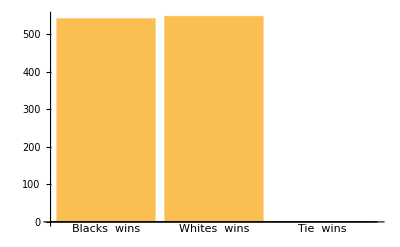

```mathematica
BarChart[Tally[exp][[All,2]],ChartLabels->Tally[exp][[All,1]]](*1089 Tries in a 9x9 size *)
```

```mathematica
exp4=Flatten[Import["exp3.xlsx"]];Length[exp4]
```

570

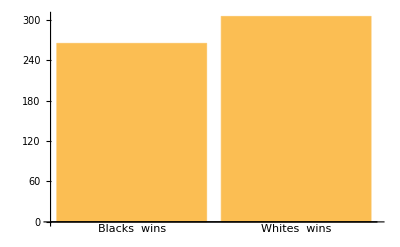

```mathematica
BarChart[Tally[exp4][[All,2]],ChartLabels->Tally[exp4][[All,1]]] (*19x19*)
```

```mathematica
hist1=Import["hist3.csv"];
```

```mathematica
hist1[[All,2]];
N[Mean[hist1[[All,2]]]]
N[Mean[hist1[[All,3]]]]
```

2886.52

2941.15

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
StudentTCI[Mean[hist1[[All,2]]],StandardDeviation[hist1[[All,2]]],Length[hist1[[All,2]]]-1]
```

{1106.14,4666.89}

```mathematica
LocationTest[{hist1[[All,2]],hist1[[All,3]]},0]
```

0.179596

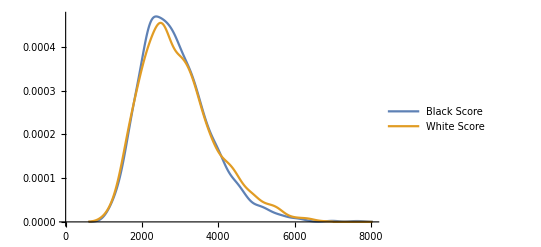

```mathematica
SmoothHistogram[{hist1[[All,2]],hist1[[All,3]]},PlotLegends->Placed[{"Black Score","White Score"},Below]]
```

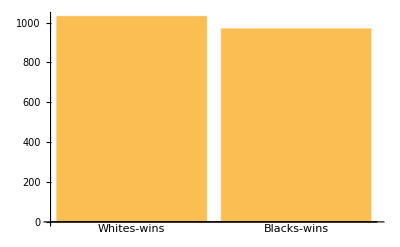

```mathematica
BarChart[Tally[hist1[[All,1]]][[All,2]],ChartLabels->Tally[hist1[[All,1]]][[All,1]]]
```

```mathematica
N[Tally[hist1[[All,1]]][[All,2]]/Total[Tally[hist1[[All,1]]][[All,2]]]]
```

{0.5155,0.4845}

```mathematica
hist1=Import["hist1.csv"];
hist2=Import["hist2.csv"];
hist3=Import["hist3.csv"];
```

```mathematica
{Tally[hist1[[All,1]]],Tally[hist2[[All,1]]],Tally[hist3[[All,1]]]}
```

{{{Blacks-wins,1053},{Whites-wins,942},{Tie-wins,5}},{{Whites-wins,1035},{Blacks-wins,962},{Tie-wins,3}},{{Whites-wins,1031},{Blacks-wins,969}}}

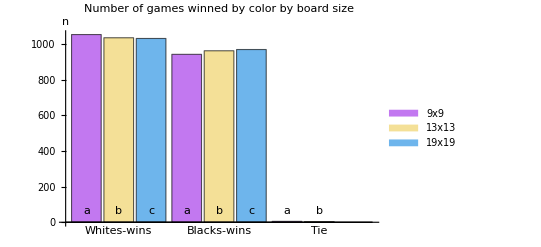

r1.eps

```mathematica
BarChart[{{1053,1035,1031},{942,962,969},{5,3,0}},ChartLabels->{Placed[{"Whites-wins","Blacks-wins","Tie"},Below],Placed[{a,b,c},Bottom]},ChartLegends->{"9x9","13x13","19x19"},ChartStyle->"Pastel",PlotLabel->"Number of games winned by color by board size",AxesLabel->{Automatic,n}]
Export["r1.eps",%]
```

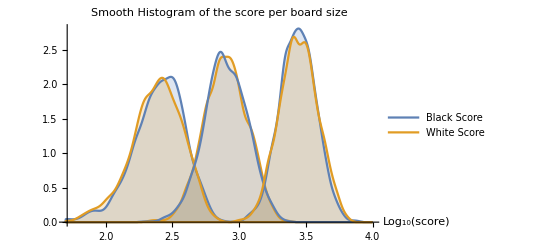

r2.eps

```mathematica
SmoothHistogram[Log[10,{{hist1[[All,2]],hist2[[All,2]],hist3[[All,2]]},{hist1[[All,3]],hist2[[All,3]],hist3[[All,3]]}}],PlotLegends->Placed[{"Black Score","White Score"},Below],Filling->Axis,PlotRange->{{1.7,4},Automatic},AxesLabel->{"Log_10(score)"},PlotLabel->"Smooth Histogram of the score per board size "]
Export["r2.eps",%]
```